```mathematica
K2meV=0.086173324;
K2eV=K2meV/1000;
```

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/FREN/order3"];
fileFFE={"e0.out.m","e0_fs.out.m","VFE.Fqh_FS.out.m","VFE.Fel_Fqh_FS.out.m"};
FFEdata=Table[ReadList[fileFFE[[i]],{Number, Number,Number,Number,Number,Number}],{i,1,4}];
```

```mathematica
FFEdata[[4]]//Dimensions
```

{4000,6}

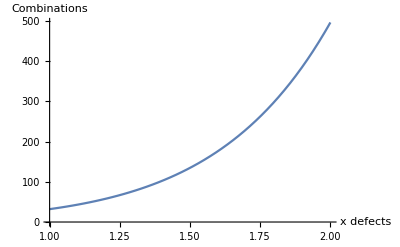

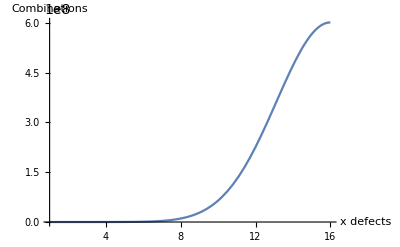

```mathematica
(*How many ways can I count x defects on 32 sites*)
f[x_]:=32!/((32-x)!*x!)
Plot[f[x],{x,1,2},AxesLabel->{"x defects","Combinations"}]
Plot[f[x],{x,1,16},AxesLabel->{"x defects","Combinations"}]
```

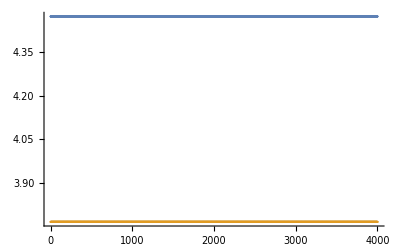

```mathematica
ListPlot@Transpose[FFEdata[[2]]][[2;;3]]
```

```mathematica
(*T_Kelvin FREN_1126_eVperD FREN_129_eVperD FREN_142_eVperD FREN_174_eVperD FREN_70_eVperD*)

(*1=1126=U4, 2=129=B2, 3=142=B3, 4=174=U3,5=70=U2 *)
```

```mathematica
FFEdata[[1]]
```

{{1,4.61969,3.93839,3.56555,4.63807,4.47583},{2,4.61969,3.93839,3.56555,4.63807,4.47583},{3,4.61969,3.93839,3.56555,4.63807,4.47583},{4,4.61969,3.93839,3.56555,4.63807,4.47583},{5,4.61969,3.93839,3.56555,4.63807,4.47583},3990,{3996,4.61969,3.93839,3.56555,4.63807,4.47583},{3997,4.61969,3.93839,3.56555,4.63807,4.47583},{3998,4.61969,3.93839,3.56555,4.63807,4.47583},{3999,4.61969,3.93839,3.56555,4.63807,4.47583},{4000,4.61969,3.93839,3.56555,4.63807,4.47583}}
 |  |  |  |

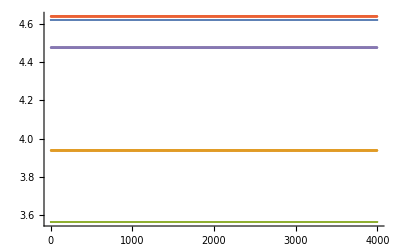

```mathematica
ListPlot@Transpose[FFEdata[[1]]][[2;;6]]
```

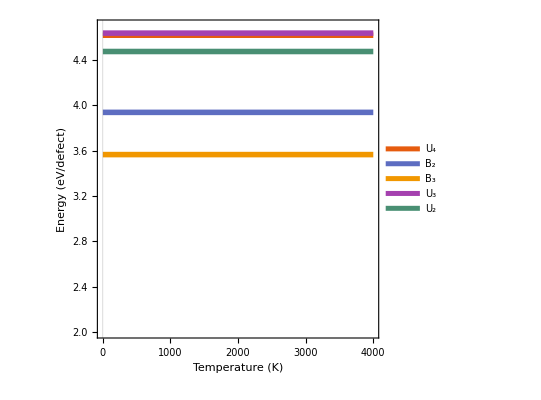

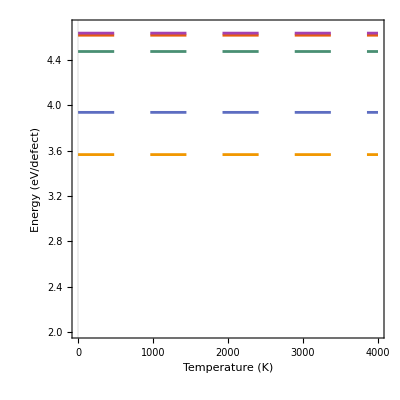

```mathematica
G1=ListLinePlot[Transpose[FFEdata[[1]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotTheme->Scientific,PlotLegends->{Style["U_4",20,Black],Style["B_2",20,Black],Style["B_3",20,Black],Style["U_3",20,Black],Style["U_2",20,Black]}]
G1a=ListLinePlot[Transpose[FFEdata[[1]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.065]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

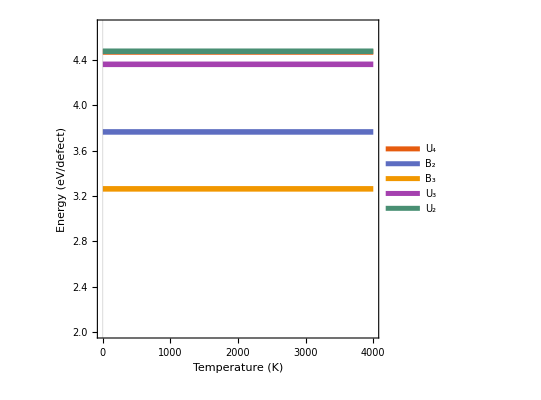

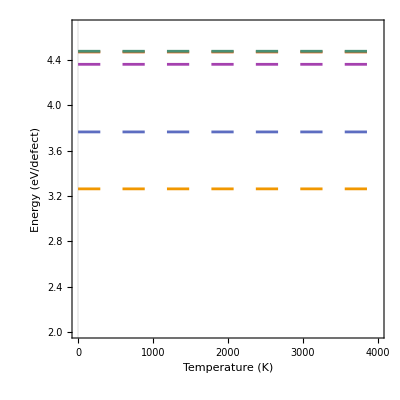

```mathematica
G2=ListLinePlot[Transpose[FFEdata[[2]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotLegends->{Style["U_4",20,Black],Style["B_2",20,Black],Style["B_3",20,Black],Style["U_3",20,Black],Style["U_2",20,Black]}]
G2a=ListLinePlot[Transpose[FFEdata[[2]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.04]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

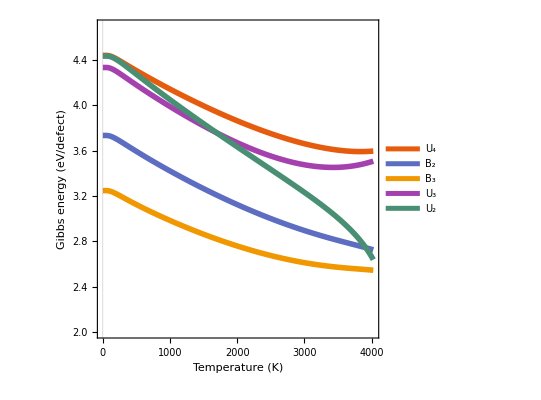

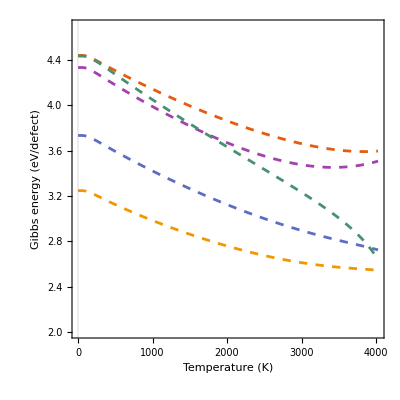

```mathematica
G3=ListLinePlot[Transpose[FFEdata[[3]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotTheme->Scientific,PlotLegends->{Style["U_4",20,Black],Style["B_2",20,Black],Style["B_3",20,Black],Style["U_3",20,Black],Style["U_2",20,Black]}]
G3a=ListLinePlot[Transpose[FFEdata[[3]]][[2;;6]],PlotRange->{Automatic,{2,4.7}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.015]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

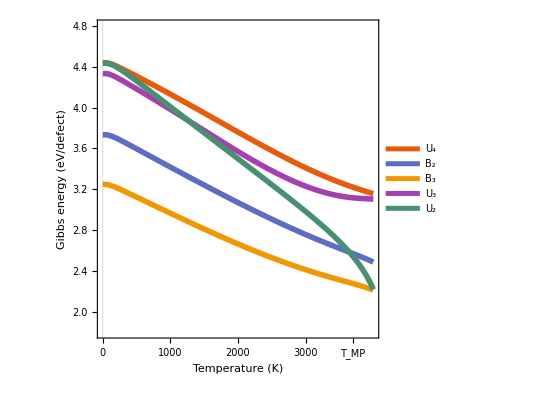

```mathematica
G4=ListLinePlot[Transpose[FFEdata[[4]]][[2;;6]],PlotRange->{Automatic,{1.8,4.8}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,FrameTicks->{Automatic,{{0,1000,2000,3000,{3700,"T_MP"}},None}},Frame->True,ImageSize->400,PlotLegends->Placed[{Style["U_4",20,Black],Style["B_2",20,Black],Style["B_3",20,Black],Style["U_3",20,Black],Style["U_2",20,Black]},{0.12,0.22}]]
G4a=ListLinePlot[Transpose[FFEdata[[4]]][[2;;6]],PlotRange->{Automatic,{1.8,4.8}},PlotTheme->Scientific,FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.015]],FrameTicksStyle->18,Frame->True,ImageSize->400];
```

```mathematica
GraphicsGrid[{{Show[G1],
Show[{G2,G1a}]},{
Show[{G3,G2a,G1a}],
Show[{G4,G3a,G2a,G1a}]}},ImageSize->1200];
```

```mathematica
(*gibbsDefects=Show[{G4,G3a,G2a,G1a},PlotRange->{{0,3000},{1.5,5}}]*)
```

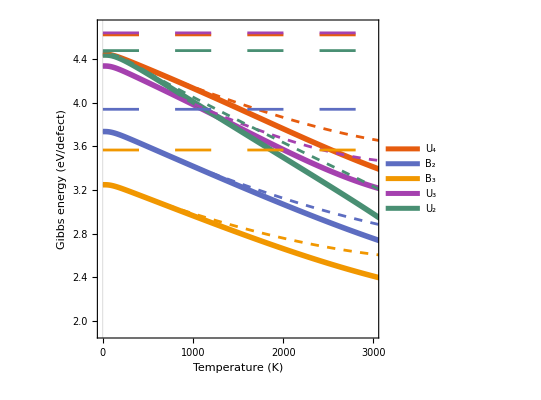

```mathematica
gibbsDefects=Show[{G4,G3a,G1a},PlotRange->{{0,3000},{1.9,4.7}}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/gibbsDefects.pdf",gibbsDefects]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/gibbsDefects.pdf

```mathematica
.
```

```mathematica
(*T_Kelvin FREN_1126_eVperD FREN_129_eVperD FREN_142_eVperD FREN_174_eVperD FREN_70_eVperD*)

(*1=1126=U4, 2=129=B2, 3=142=B3, 4=174=U3,5=70=U2 *)
```

```mathematica
(*T_Kelvin FREN_1126_eVperD FREN_129_eVperD FREN_142_eVperD FREN_174_eVperD FREN_70_eVperD*)
```

```mathematica
gibbsData=FFEdata[[4]];
mB3=24;
mB2=24;
mU2=3;
mU3=12;
mU4=12;
temperature=Transpose[gibbsData][[1]];
gibbsU4=Transpose[gibbsData][[2]];
gibbsB2=Transpose[gibbsData][[3]];
gibbsB3=Transpose[gibbsData][[4]];
gibbsU3=Transpose[gibbsData][[5]];
gibbsU2=Transpose[gibbsData][[6]];

(*1126=U4, 129=B2, 142=B3, 174=U3, 70=U2*)
```

```mathematica
Exp[-4/(K2eV*300)]
```

6.35259×10^-68

ListLinePlot::prng: Value of option PlotRange -> {Auto,{1/1000000000000000000000000000000000000000000000000000000000000,1/100000000000000000000000000000000000000000000000000}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

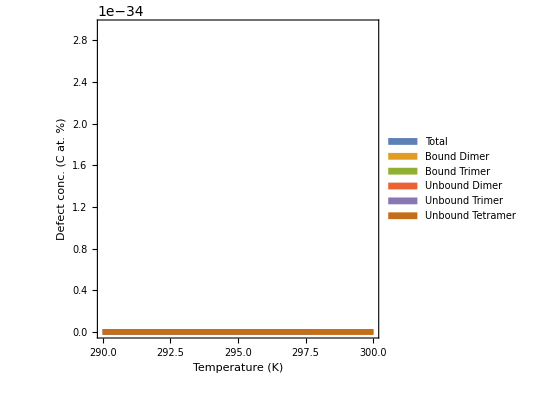

```mathematica
upper=300;
lower=290;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};


p7=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.09],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["Temperature (K)",18,Black],Style["Defect conc. (C at. %)",18,Black]},Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["Total",18,Black],Style["Bound Dimer",18,Black],Style["Bound Trimer",18,Black],Style["Unbound Dimer",18,Black],Style["Unbound Trimer",18,Black],Style["Unbound Tetramer",18,Black]}],{0.3,0.75}],AspectRatio->1,PlotRange->{Auto,{10^-60,10^-50}}]
```

{U_4,B_2,B_3,U_3,U_2}

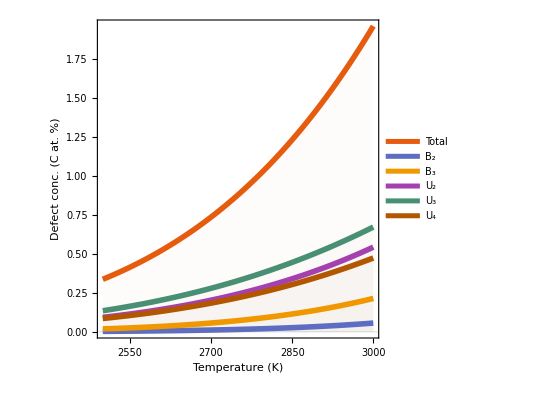

```mathematica
upper=3000;
lower=2500;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};

{Style["U_4",20,Black],Style["B_2",20,Black],Style["B_3",20,Black],Style["U_3",20,Black],Style["U_2",20,Black]}
p5=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["Temperature (K)",18,Black],Style["Defect conc. (C at. %)",18,Black]},PlotTheme->Scientific,Frame->True,ImageSize->400,PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.3,0.75}],AspectRatio->1,PlotRange->All]
```

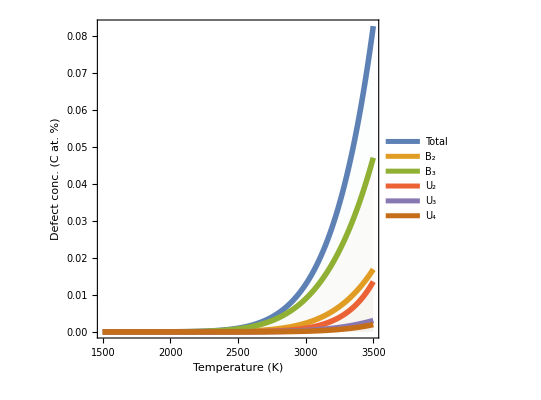

```mathematica
upper=3500;
lower=1500;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];

concB2=Transpose@{rangeT,100*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*Exp[-(rangeGibbsU4)/(K2eV*rangeT)]};

concU2=Transpose@{rangeT,100*Exp[-(rangeGibbsU2)/(K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*Exp[-(rangeGibbsU3)/(K2eV*rangeT)]};


concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p6=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["Temperature (K)",18,Black],Style["Defect conc. (C at. %)",18,Black]},Frame->True,ImageSize->400,PlotLegends->{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},AspectRatio->1,PlotRange->All]
```

```mathematica
styles=Flatten@Join[{Directive[{Thickness[0.008]}],Table[Directive[{Thickness[0.01],Dashing[{0.02*i,0.04}]}],{i,1,3}],Directive[{Thickness[0.008],Dotted}],Directive[{Thickness[0.01],DotDashed}]}]
```

{Directive[{Thickness[0.008]}],Directive[{Thickness[0.01],Dashing[{0.02,0.04}]}],Directive[{Thickness[0.01],Dashing[{0.04,0.04}]}],Directive[{Thickness[0.01],Dashing[{0.06,0.04}]}],Directive[{Thickness[0.008],Dashing[{0,Small}]}],Directive[{Thickness[0.01],Dashing[{0,Small,Small,Small}]}]}

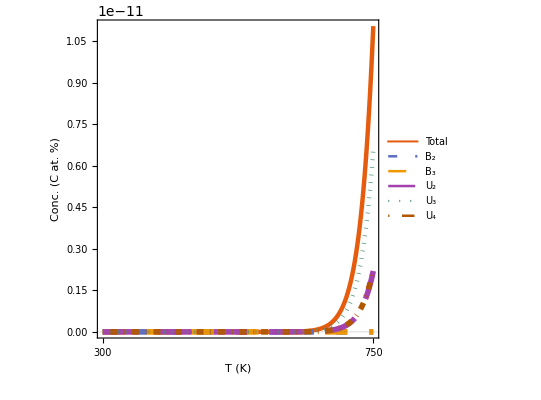

```mathematica
upper=750;
lower=300;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p0=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Conc. (C at. %)",18,Black]},Frame->True,ImageSize->400,PlotTheme->Scientific,PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.25,0.55}],AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{300,750},None}}]
```

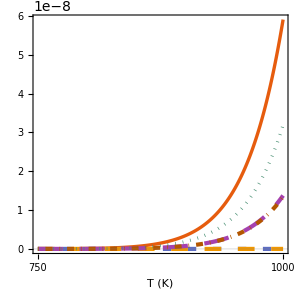

```mathematica
upper=1000;
lower=750;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p1=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->300,PlotTheme->Scientific,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{750,1000},None}}]
```

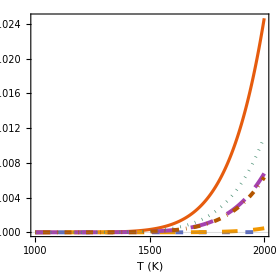

```mathematica
upper=2000;
lower=1000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p2=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->280,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{1000,1500,2000},None}}]
```

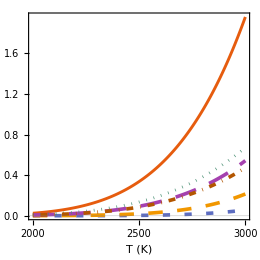

```mathematica
upper=3000;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
p3=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->260,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

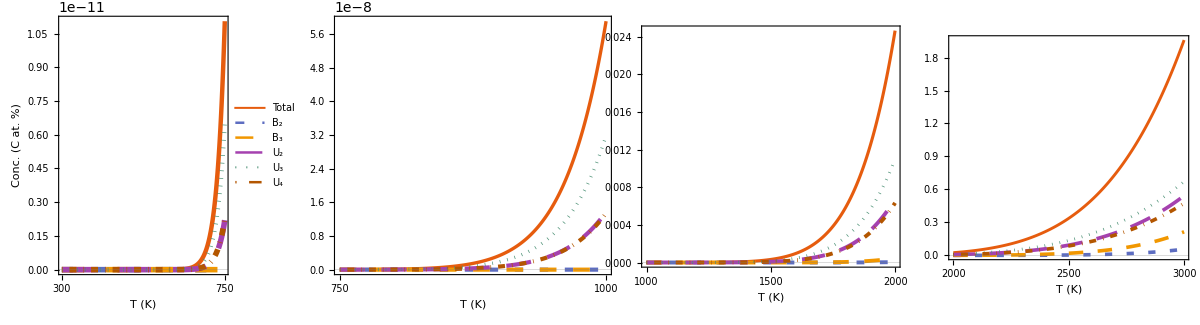

```mathematica
concDefects=GraphicsGrid[{{p0,p1,p2,p3}},ImageSize->1200,Spacings->-25]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefects.pdf",concDefects]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefects.pdf

#### Log defects

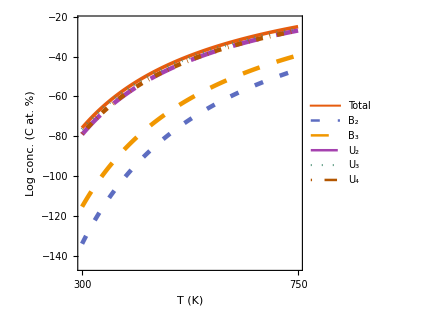

```mathematica
upper=750;
lower=300;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
l0=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Log conc. (C at. %)",18,Black]},Frame->True,ImageSize->320,PlotTheme->Scientific,PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.75,0.32}],AspectRatio->1,PlotRange->{Automatic,{-145,-22}},FrameTicks->{{Automatic,None},{{300,750},None}}]
```

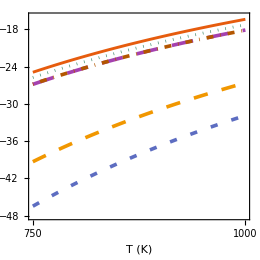

```mathematica
upper=1000;
lower=750;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
l1=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->260,PlotTheme->Scientific,AspectRatio->1,PlotRange->{Automatic,{-48,-16}},FrameTicks->{{Automatic,None},{{750,1000},None}}]
```

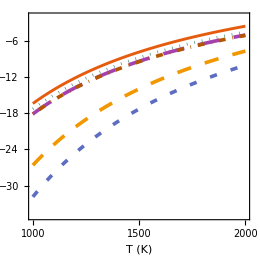

```mathematica
upper=2000;
lower=1000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
l2=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->260,AspectRatio->1,PlotRange->{Automatic,{-35,-2}},FrameTicks->{{Automatic,None},{{1000,1500,2000},None}}]
```

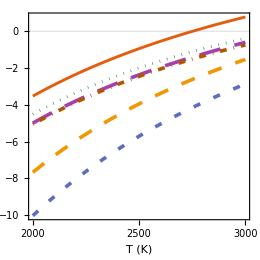

```mathematica
upper=3000;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
l3=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["",18,Black]},Frame->True,ImageSize->260,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

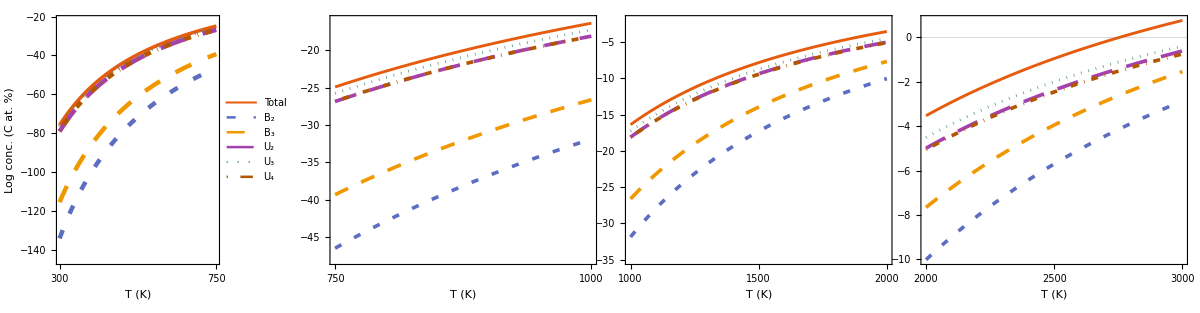

```mathematica
logConcDefects=GraphicsGrid[{{l0,l1,l2,l3}},ImageSize->1200,Spacings->-15]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/logConcDefects.pdf",logConcDefects]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/logConcDefects.pdf

#### Mixed log and normal conc defects

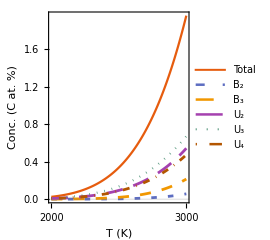

```mathematica
upper=3000;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[concB2][[2]]+Transpose[concB3][[2]]+Transpose[concU2][[2]]+Transpose[concU3][[2]]+Transpose[concU4][[2]]}]};
q1=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.25,0.55}],PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Conc. (C at. %)",18,Black]},Frame->True,ImageSize->{200,200},AspectRatio->1.2,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

```mathematica
{concTotal[[1]],concB2[[1]],concB3[[1]],concU2[[1]],concU3[[1]],concU4[[1]]}//TableForm
{concTotal[[1]],concB2[[1]]+concB3[[1]],concU2[[1]]+concU3[[1]]+concU4[[1]]}//TableForm
```

2000 | 0.0246479
2000 | 0.0000443762
2000 | 0.000469729
2000 | 0.00677429
2000 | 0.0110218
2000 | 0.00633773

2000 | 0.0246479
4000 | 0.000514105
6000 | 0.0241338

```mathematica
{concTotal[[501]],concB2[[501]],concB3[[501]],concU2[[501]],concU3[[501]],concU4[[501]]}//TableForm
{concTotal[[501]],concB2[[501]]+concB3[[1]],concU2[[501]]+concU3[[501]]+concU4[[501]]}//TableForm
```

2500 | 0.336943
2500 | 0.00332932
2500 | 0.0192506
2500 | 0.0931655
2500 | 0.135424
2500 | 0.0857742

2500 | 0.336943
4500 | 0.00379905
7500 | 0.314363

```mathematica
{concTotal[[-1]],concB2[[-1]],concB3[[-1]],concU2[[-1]],concU3[[-1]],concU4[[-1]]}//TableForm
{concTotal[[-1]],concB2[[-1]]+concB3[[-1]],concU2[[-1]]+concU3[[-1]]+concU4[[-1]]}//TableForm
```

3000 | 1.95916
3000 | 0.0564714
3000 | 0.214447
3000 | 0.543088
3000 | 0.671683
3000 | 0.473473

3000 | 1.95916
6000 | 0.270918
9000 | 1.68824

```mathematica
styles;
```

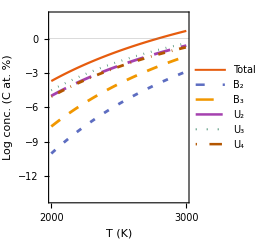

```mathematica
upper=3000;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
q2=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.78,0.255}],PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Log conc. (C at. %)",18,Black]},Frame->True,ImageSize->{200,186},AspectRatio->1.2,PlotRange->{All,{-14,2}},FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

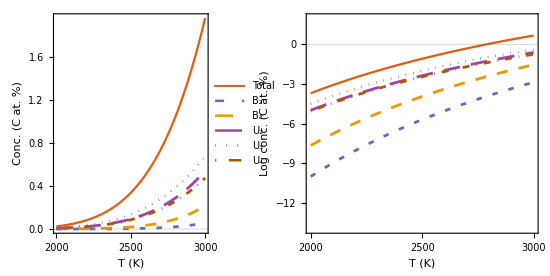

```mathematica
concDefectsLog=GraphicsGrid[{{q1,q2}},Spacings->-30,ImageSize->550]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefectsLog.pdf",concDefectsLog]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefectsLog.pdf

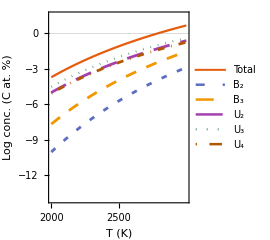

```mathematica
upper=3000;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsB2=gibbsB2[[lower;;upper]];
rangeGibbsB3=gibbsB3[[lower;;upper]];
rangeGibbsU3=gibbsU3[[lower;;upper]];
rangeGibbsU2=gibbsU2[[lower;;upper]];
rangeGibbsU4=gibbsU4[[lower;;upper]];
concB2=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,Log[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concU2=Transpose@{rangeT,Log[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,Log[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,Log[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concTotal=Transpose@{rangeT,Log[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]+100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]+100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]+100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]+100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
q20p=ListLinePlot[{concTotal,concB2,concB3,concU2,concU3,concU4},PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.78,0.30}],PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameTicks->{{Automatic,None},{{2000,2250,2500,2750},None}},FrameLabel->{Style["T (K)",18,Black],Style["Log conc. (C at. %)",18,Black]},Frame->True,ImageSize->{200,186},AspectRatio->1.2,PlotRange->{All,{-14,1.5}},FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

## Rescaling

Rescaling from 2-fp_conc_vacancies.nb

```mathematica
bound2perc[x_]:=1.6206574519315155*^-16+0.9803921568627428 x+9.738148874506295*^-15 x^2-1.1748947532028086*^-14 x^3+6.215029063473273*^-15 x^4-1.2218837714642487*^-15 x^5;
bound5perc[x_]:=8.103287259657577*^-17+0.9523809523809508 x+7.663032589865555*^-15 x^2-9.353369984591884*^-15 x^3+5.006385894032757*^-15 x^4-9.925018773205514*^-16 x^5;
bound10perc[x_]:=3.241314903863031*^-16+0.9090909090909071 x+1.037813755583137*^-14 x^2-1.2316293967438529*^-14 x^3+6.269552938789279*^-15 x^4-1.1892822218456837*^-15 x^5;
```

```mathematica
unbound2perc[x_]:=-5.049764021013934*^-6+0.00028406881403112273 x+0.4763535598668431 x^2+0.02176144071657942 x^3-0.18220004343099838 x^4+0.09325564512342163 x^5-0.00108431400048166 x^6-0.01653414895266638 x^7+0.006318465020616935 x^8-0.0007840493862185255 x^9;
unbound5perc[x_]:=1.2970443363177379*^-8-7.28466968974883*^-7 x+0.18050994187449548 x^2-0.00005780456837115145 x^3-0.0070248862158602205 x^4-0.0003150406448858535 x^5+0.0008850432367642691 x^6-0.00021060375608836354 x^7+0.000011794014320998825 x^8+1.2213243973184373*^-6 (x^9)^5;
unbound10perc[x_]:=3.2971772330956747*^-12-1.5068606876591106*^-10 x+0.08100000149351187 x^2-4.638081159766825*^-9 x^3-0.000801901715180822 x^4+4.161895485125644*^-8 x^5+0.000014393448729948308 x^6+1.359105353571275*^-7 x^7-4.2629142497908376*^-7 x^8+4.1546673339818885*^-8 x^9;
```

```mathematica
f[x_]:=2x;
```

#### 2percent rescaled

```mathematica
twoPconcB2=Transpose@{rangeT,bound2perc[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};

twoPconcB3=Transpose@{rangeT,bound2perc[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};

twoPconcU2=Transpose@{rangeT,unbound2perc[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};

twoPconcU3=Transpose@{rangeT,unbound2perc[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};

twoPconcU4=Transpose@{rangeT,unbound2perc[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
```

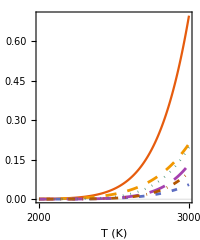

```mathematica
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[twoPconcB2][[2]]+Transpose[twoPconcB3][[2]]+Transpose[twoPconcU2][[2]]+Transpose[twoPconcU3][[2]]+Transpose[twoPconcU4][[2]]}]};
q12p=ListLinePlot[{concTotal,twoPconcB2,twoPconcB3,twoPconcU2,twoPconcU3,twoPconcU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Conc. (C at. %)",18,Black]},Frame->True,ImageSize->{200,200},AspectRatio->1.2,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

```mathematica
{concTotal[[1]],twoPconcB2[[1]],twoPconcB3[[1]],twoPconcU2[[1]],twoPconcU3[[1]],twoPconcU4[[1]]}//TableForm
{concTotal[[1]],twoPconcB2[[1]]+twoPconcB3[[1]],twoPconcU2[[1]]+twoPconcU3[[1]]+twoPconcU4[[1]]}//TableForm
```

2000 | 0.00059463
2000 | 0.000043506
2000 | 0.000460518
2000 | 0.0000187413
2000 | 0.0000559752
2000 | 0.0000158894

2000 | 0.00059463
4000 | 0.000504024
6000 | 0.0000906059

```mathematica
{concTotal[[501]],twoPconcB2[[501]],twoPconcB3[[501]],twoPconcU2[[501]],twoPconcU3[[501]],twoPconcU4[[501]]}//TableForm
{concTotal[[501]],twoPconcB2[[501]]+twoPconcB3[[501]],twoPconcU2[[501]]+twoPconcU3[[501]]+twoPconcU4[[501]]}//TableForm
```

2500 | 0.0385926
2500 | 0.00326404
2500 | 0.0188732
2500 | 0.0041606
2500 | 0.00876654
2500 | 0.00352826

2500 | 0.0385926
5000 | 0.0221372
7500 | 0.0164554

```mathematica
{concTotal[[-1]],twoPconcB2[[-1]],twoPconcB3[[-1]],twoPconcU2[[-1]],twoPconcU3[[-1]],twoPconcU4[[-1]]}//TableForm
{concTotal[[-1]],twoPconcB2[[-1]]+twoPconcB3[[-1]],twoPconcU2[[-1]]+twoPconcU3[[-1]]+twoPconcU4[[-1]]}//TableForm
```

3000 | 0.696761
3000 | 0.0553641
3000 | 0.210242
3000 | 0.132475
3000 | 0.196476
3000 | 0.102204

3000 | 0.696761
6000 | 0.265606
9000 | 0.431154

#### Log conc

```mathematica
twoPconcB2=Transpose@{rangeT,Log@bound2perc[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};

twoPconcB3=Transpose@{rangeT,Log@bound2perc[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};

twoPconcU2=Transpose@{rangeT,Log@unbound2perc[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};

twoPconcU3=Transpose@{rangeT,Log@unbound2perc[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};

twoPconcU4=Transpose@{rangeT,Log@unbound2perc[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
```

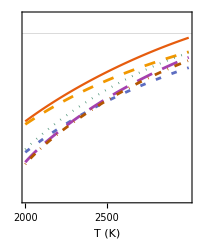

```mathematica
concTotal=Transpose@{rangeT,Log[bound2perc[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]+bound2perc[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]+unbound2perc[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]+unbound2perc[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]+unbound2perc[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]]};
q22p=ListLinePlot[{concTotal,twoPconcB2,twoPconcB3,twoPconcU2,twoPconcU3,twoPconcU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameTicks->{{None,None},{{2000,2250,2500,2750},None}},FrameLabel->{Style["T (K)",18,Black],Style[" ",18,Black]},Frame->True,ImageSize->{200,186},AspectRatio->1.2,PlotRange->{All,{-14,1.5}},FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

#### Five percent

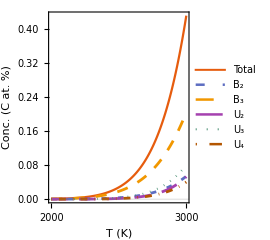

```mathematica
fivePconcB2=Transpose@{rangeT,bound5perc[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};

fivePconcB3=Transpose@{rangeT,bound5perc[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};

fivePconcU2=Transpose@{rangeT,unbound5perc[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};

fivePconcU3=Transpose@{rangeT,unbound5perc[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};

fivePconcU4=Transpose@{rangeT,unbound5perc[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[fivePconcB2][[2]]+Transpose[fivePconcB3][[2]]+Transpose[fivePconcU2][[2]]+Transpose[fivePconcU3][[2]]+Transpose[fivePconcU4][[2]]}]};
q15p=ListLinePlot[{concTotal,fivePconcB2,fivePconcB3,fivePconcU2,fivePconcU3,fivePconcU4},PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.25,0.55}],PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Conc. (C at. %)",18,Black]},Frame->True,ImageSize->{200,200},AspectRatio->1.2,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

```mathematica
{concTotal[[1]],fivePconcB2[[1]],fivePconcB3[[1]],fivePconcU2[[1]],fivePconcU3[[1]],fivePconcU4[[1]]}//TableForm
{concTotal[[1]],fivePconcB2[[1]]+fivePconcB3[[1]],fivePconcU2[[1]]+fivePconcU3[[1]]+fivePconcU4[[1]]}//TableForm
```

2000 | 0.000527107
2000 | 0.000042263
2000 | 0.000447361
2000 | 8.29178×10^-6
2000 | 0.0000219331
2000 | 7.25883×10^-6

2000 | 0.000527107
4000 | 0.000489624
6000 | 0.0000374837

```mathematica
{concTotal[[501]],fivePconcB2[[501]],fivePconcB3[[501]],fivePconcU2[[501]],fivePconcU3[[501]],fivePconcU4[[501]]}//TableForm
{concTotal[[501]],fivePconcB2[[501]]+fivePconcB3[[501]],fivePconcU2[[501]]+fivePconcU3[[501]]+fivePconcU4[[1]]}//TableForm
```

2500 | 0.0277063
2500 | 0.00317078
2500 | 0.0183339
2500 | 0.00156616
2500 | 0.00330787
2500 | 0.00132758

2500 | 0.0277063
5000 | 0.0215047
7000 | 0.00488129

```mathematica
{concTotal[[-1]],fivePconcB2[[-1]],fivePconcB3[[-1]],fivePconcU2[[-1]],fivePconcU3[[-1]],fivePconcU4[[-1]]}//TableForm
{concTotal[[-1]],fivePconcB2[[-1]]+fivePconcB3[[-1]],fivePconcU2[[-1]]+fivePconcU3[[-1]]+fivePconcU4[[-1]]}//TableForm
```

3000 | 0.430767
3000 | 0.0537823
3000 | 0.204235
3000 | 0.0526246
3000 | 0.0800164
3000 | 0.040108

3000 | 0.430767
6000 | 0.258018
9000 | 0.172749

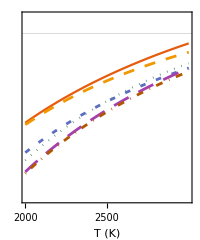

```mathematica
fivePconcB2=Transpose@{rangeT,Log@bound5perc[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};

fivePconcB3=Transpose@{rangeT,Log@bound5perc[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};

fivePconcU2=Transpose@{rangeT,Log@unbound5perc[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};

fivePconcU3=Transpose@{rangeT,Log@unbound5perc[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};

fivePconcU4=Transpose@{rangeT,Log@unbound5perc[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Log[bound5perc[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]+bound5perc[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]+unbound5perc[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]+unbound5perc[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]+unbound5perc[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]]};
q25p=ListLinePlot[{concTotal,fivePconcB2,fivePconcB3,fivePconcU2,fivePconcU3,fivePconcU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameTicks->{{None,None},{{2000,2250,2500,2750},None}},FrameLabel->{Style["T (K)",18,Black],None},Frame->True,ImageSize->{200,186},AspectRatio->1.2,PlotRange->{All,{-14,1.5}},FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

### ten percent

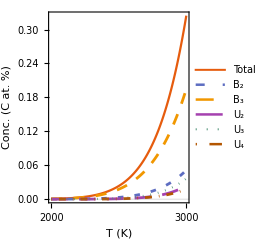

```mathematica
tenPconcB2=Transpose@{rangeT,bound10perc[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};

tenPconcB3=Transpose@{rangeT,bound10perc[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};

tenPconcU2=Transpose@{rangeT,unbound10perc[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};

tenPconcU3=Transpose@{rangeT,unbound10perc[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};

tenPconcU4=Transpose@{rangeT,unbound10perc[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Flatten@Transpose[{Transpose[tenPconcB2][[2]]+Transpose[tenPconcB3][[2]]+Transpose[tenPconcU2][[2]]+Transpose[tenPconcU3][[2]]+Transpose[tenPconcU4][[2]]}]};
q110p=ListLinePlot[{concTotal,tenPconcB2,tenPconcB3,tenPconcU2,tenPconcU3,tenPconcU4},PlotLegends->Placed[{Style["Total",18,Black],Style["B_2",18,Black],Style["B_3",18,Black],Style["U_2",18,Black],Style["U_3",18,Black],Style["U_4",18,Black]},{0.25,0.55}],PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["T (K)",18,Black],Style["Conc. (C at. %)",18,Black]},Frame->True,ImageSize->{200,200},AspectRatio->1.2,PlotRange->All,FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

```mathematica
{concTotal[[1]],tenPconcB2[[1]],tenPconcB3[[1]],tenPconcU2[[1]],tenPconcU3[[1]],tenPconcU4[[1]]}//TableForm
{concTotal[[1]],tenPconcB2[[1]]+tenPconcB3[[1]],tenPconcU2[[1]]+tenPconcU3[[1]]+tenPconcU4[[1]]}//TableForm
```

2000 | 0.000484179
2000 | 0.000040342
2000 | 0.000427026
2000 | 3.71717×10^-6
2000 | 9.83988×10^-6
2000 | 3.25351×10^-6

2000 | 0.000484179
4000 | 0.000467368
6000 | 0.0000168106

```mathematica
{concTotal[[-501]],tenPconcB2[[-501]],tenPconcB3[[-501]],tenPconcU2[[-501]],tenPconcU3[[-501]],tenPconcU4[[-501]]}//TableForm
{concTotal[[-501]],tenPconcB2[[-501]]+tenPconcB3[[-501]],tenPconcU2[[-501]]+tenPconcU3[[-501]]+tenPconcU4[[-501]]}//TableForm
```

2500 | 0.0233114
2500 | 0.00302666
2500 | 0.0175006
2500 | 0.000703004
2500 | 0.00148524
2500 | 0.000595891

2500 | 0.0233114
5000 | 0.0205272
7500 | 0.00278413

```mathematica
{concTotal[[-1]],tenPconcB2[[-1]],tenPconcB3[[-1]],tenPconcU2[[-1]],tenPconcU3[[-1]],tenPconcU4[[-1]]}//TableForm
{concTotal[[-1]],tenPconcB2[[-1]]+tenPconcB3[[-1]],tenPconcU2[[-1]]+tenPconcU3[[-1]]+tenPconcU4[[-1]]}//TableForm
```

3000 | 0.324611
3000 | 0.0513376
3000 | 0.194952
3000 | 0.0238211
3000 | 0.0363819
3000 | 0.0181182

3000 | 0.324611
6000 | 0.246289
9000 | 0.0783212

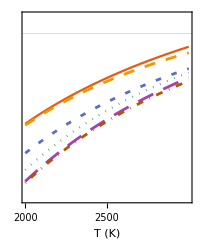

```mathematica
tenPconcB2=Transpose@{rangeT,Log@bound10perc[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]};
concB2=Transpose@{rangeT,100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]};

tenPconcB3=Transpose@{rangeT,Log@bound10perc[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]};
concB3=Transpose@{rangeT,100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]};

tenPconcU2=Transpose@{rangeT,Log@unbound10perc[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]};
concU2=Transpose@{rangeT,100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]};

tenPconcU3=Transpose@{rangeT,Log@unbound10perc[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]};
concU3=Transpose@{rangeT,100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]};

tenPconcU4=Transpose@{rangeT,Log@unbound10perc[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]};
concU4=Transpose@{rangeT,100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]};
concTotal=Transpose@{rangeT,Log[bound10perc[100*mB2*Exp[-(rangeGibbsB2)/(K2eV*rangeT)]]+bound10perc[100*mB3*Exp[-(rangeGibbsB3)/(K2eV*rangeT)]]+unbound10perc[100*mU2^0.5*Exp[-(rangeGibbsU2)/(2*K2eV*rangeT)]]+unbound10perc[100*mU3^0.5*Exp[-(rangeGibbsU3)/(2*K2eV*rangeT)]]+unbound10perc[100*mU4^0.5*Exp[-(rangeGibbsU4)/(2*K2eV*rangeT)]]]};
q210p=ListLinePlot[{concTotal,tenPconcB2,tenPconcB3,tenPconcU2,tenPconcU3,tenPconcU4},PlotStyle->styles,FrameStyle->Directive[Thickness[0.008]],PlotTheme->Scientific,FillingStyle->Opacity[0.015],FrameTicksStyle->Directive[18,Black],FrameTicks->{{None,None},{{2000,2250,2500,2750},None}},FrameLabel->{Style["T (K)",18,Black],None},Frame->True,ImageSize->{200,186},AspectRatio->1.2,PlotRange->{All,{-14,1.5}},FrameTicks->{{Automatic,None},{{2000,2500,3000},None}}]
```

-Graphics-

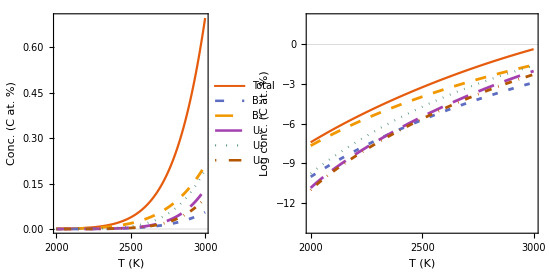

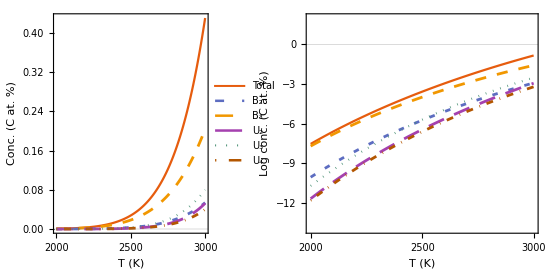

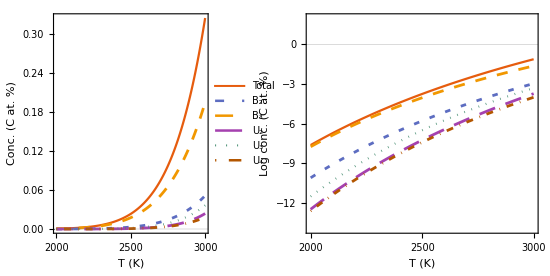

```mathematica
concDefectsLog=GraphicsGrid[{{q1,q2}},Spacings->-30,ImageSize->550]
concDefectsLog2=GraphicsGrid[{{q12p,q22p}},Spacings->-30,ImageSize->550]
concDefectsLog5=GraphicsGrid[{{q15p,q25p}},Spacings->-30,ImageSize->550]
concDefectsLog10=GraphicsGrid[{{q110p,q210p}},Spacings->-30,ImageSize->550]
```

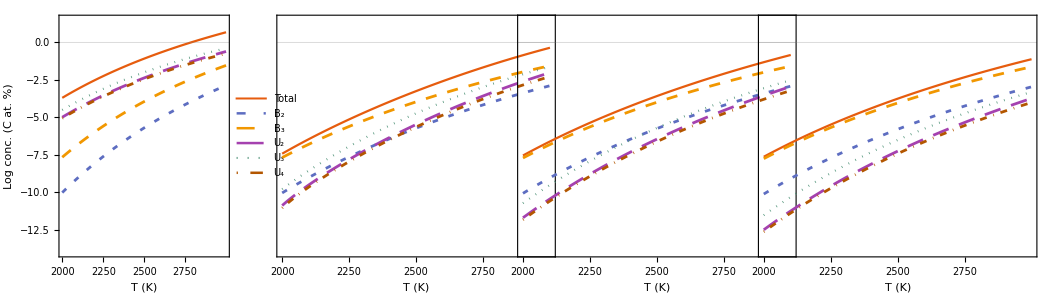

```mathematica
concDefectsLogSub=GraphicsGrid[{{q20p,q22p,q25p,q210p}},Spacings->-53,ImageSize->1050]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefectsLogSub.pdf",concDefectsLogSub]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/concDefectsLogSub.pdf

#### Sanity check

The approximate version is that n_fp =(n_fp_0)^2/(n_fp+n_0)

```mathematica
soln=With[{n0=0.05},Solve[nfp==(nfp0^2)/(nfp+n0),nfp]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{nfp→0.05 (-1.-1. √(1.+400. nfp0^2))},{nfp→0.05 (-1.+√(1.+400. nfp0^2))}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

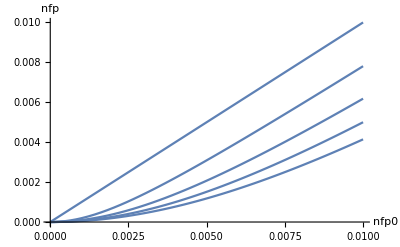

```mathematica
Plot[Table[nfp/.With[{n0=c},Solve[nfp==(nfp0^2)/(nfp+n0),nfp]][[2]],{c,0,0.02,0.005}],{nfp0,0,0.01},AxesLabel->{"nfp0","nfp"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

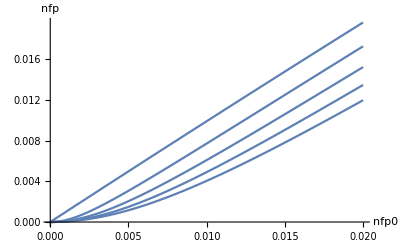

```mathematica
Plot[Table[nfp/.With[{n0=c},Solve[nfp==(nfp0^2)*(1-n0-2nfp)/(nfp+n0),nfp]][[2]],{c,0,0.02,0.005}],{nfp0,0,0.02},AxesLabel->{"nfp0","nfp"}]
```

```mathematica
data=Table[Table[{n0,(nfp/.Solve[nfp==(nfp0^2)*(1-n0-2nfp)/(nfp+n0),nfp])[[2]]},{n0,0.00001,0.1,0.001}],{nfp0,0.00000001,0.026,0.005}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

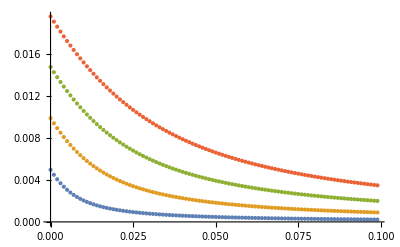

```mathematica
ListPlot[data[[2;;5]],PlotRange->All]
```

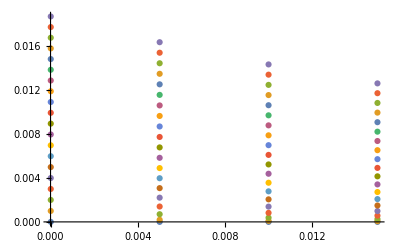

```mathematica
ListPlot@data
```

```mathematica
D[x*Log[x],x]
```

1+Log[x]

```mathematica
D[(1-x)*Log[(1-x)],x]
```

-1-Log[1-x]

```mathematica
data=Table[Table[{n0,(nfp/.Solve[nfp==(nfp0^2)*(1-n0-2nfp)/(nfp+n0),nfp])[[2]]},{n0,0.00001,0.1,0.001}],{nfp0,0.00000001,0.026,0.005}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
data2=Table[Table[{n0,(nfp/.Solve[nfp==(nfp0^2)*(1-n0-2nfp)^4/((nfp+n0)*(1-n0-nfp)*(1-nfp)),nfp])[[2]]},{n0,0.00001,0.1,0.001}],{nfp0,0.00000001,0.026,0.005}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

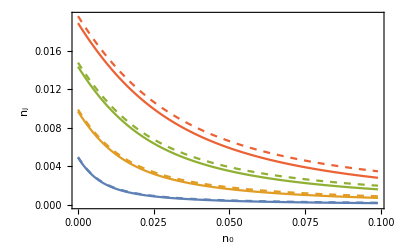

```mathematica
imag=Show[{ListLinePlot[data[[2;;5]],PlotRange->All,PlotStyle->Dashed,Frame->True,FrameLabel->{Style["n_0",20],Style["n_j",20]}],ListLinePlot[data2[[2;;5]],PlotRange->All]}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/frenkel-conc-vs-vac-conc-comparison4th-2nd.pdf",imag]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/frenkel-conc-vs-vac-conc-comparison4th-2nd.pdf

```mathematica
mat={{aa,bb,cc},{dd,ee,ff},{gg,hh,ii}}
```

{{aa,bb,cc},{dd,ee,ff},{gg,hh,ii}}

```mathematica
mat^2
```

{{aa^2,bb^2,cc^2},{dd^2,ee^2,ff^2},{gg^2,hh^2,ii^2}}

```mathematica
Det[mat]
```

-cc ee gg+bb ff gg+cc dd hh-aa ff hh-bb dd ii+aa ee ii

```mathematica
mat2={{1,2,3},{5,6,7},{12,23,34}}
mat3={{11,21,31},{51,61,71},{12,23,34}}
```

{{1,2,3},{5,6,7},{12,23,34}}

{{11,21,31},{51,61,71},{12,23,34}}

```mathematica
mat2//Dimensions
```

{3,3}

```mathematica
Eigenvalues[2*mat3]//N
```

{211.186,0.81445,0.}

```mathematica
Eigenvalues[mat3]//N
```

{105.593,0.407225,0.}

```mathematica
Norm/@Eigenvectors[mat3]//N
```

{2.96379,2.35488,2.44949}

```mathematica
Norm/@Eigenvectors[mat2]//N
```

{1.02733,1.8114,2.44949}

```mathematica
mat2/mat3
```

{{1/11,2/21,3/31},{5/51,6/61,7/71},{1,1,1}}

```mathematica
Norm[mat2/45]//N
```

0.980615

```mathematica
Norm@mat2//N
```

44.1277

```mathematica
Norm@mat2//N
Norm@mat3//N
```

44.1277

120.702

```mathematica
s=(Norm@mat2//N)/(Norm@mat3//N)
Norm@(s*mat3)//N
```

0.365591

44.1277